```mathematica
Exit[]
```

```mathematica
Directory[]
```

/home/rlewis/Dropbox/lean/mm_lean

```mathematica
(* If you are not in the mm_lean directory already,  you should be *)SetDirectory["~/mm_lean"]
```

```mathematica
<<"main.m"
<<"_target/deps/mathematica/lean_form.m"
```

```mathematica
ProveUsingLeanTactic[ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover"]
```

fun (h : Prop) (h_1 : Prop) (h_2 : Prop) (h_3 : h -> h_1 -> h_2) (h_4 : and h h_1), (h_3 (and.left h h_1 h_4) (and.right h h_1 h_4))

```mathematica
ProveUsingLeanTactic[ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover",True]
```

LeanLambda[LeanNameMkString["h", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_1", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_2", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_3", LeanNameAnonymous], BinderInfoDefault, LeanPi[LeanNameMkString["a", LeanNameAnonymous], BinderInfoDefault, LeanVar[2], LeanPi[LeanNameMkString["a", LeanNameAnonymous], BinderInfoDefault, LeanVar[2], LeanVar[2]]], LeanLambda[LeanNameMkString["h_4", LeanNameAnonymous], BinderInfoDefault, LeanApp[LeanApp[LeanConst[LeanNameMkString["and", LeanNameAnonymous], LeanLevelListNil], LeanVar[3]], LeanVar[2]], LeanApp[LeanApp[LeanVar[1], LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["left", LeanNameMkString["and", LeanNameAnonymous]], LeanLevelListNil], LeanVar[4]], LeanVar[3]], LeanVar[0]]], LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["right", LeanNameMkString["and", LeanNameAnonymous]], LeanLevelListNil], LeanVar[4]], LeanVar[3]], LeanVar[0]]]]]]]]

```mathematica
<<"natural_deduction_graphs.wl"
```

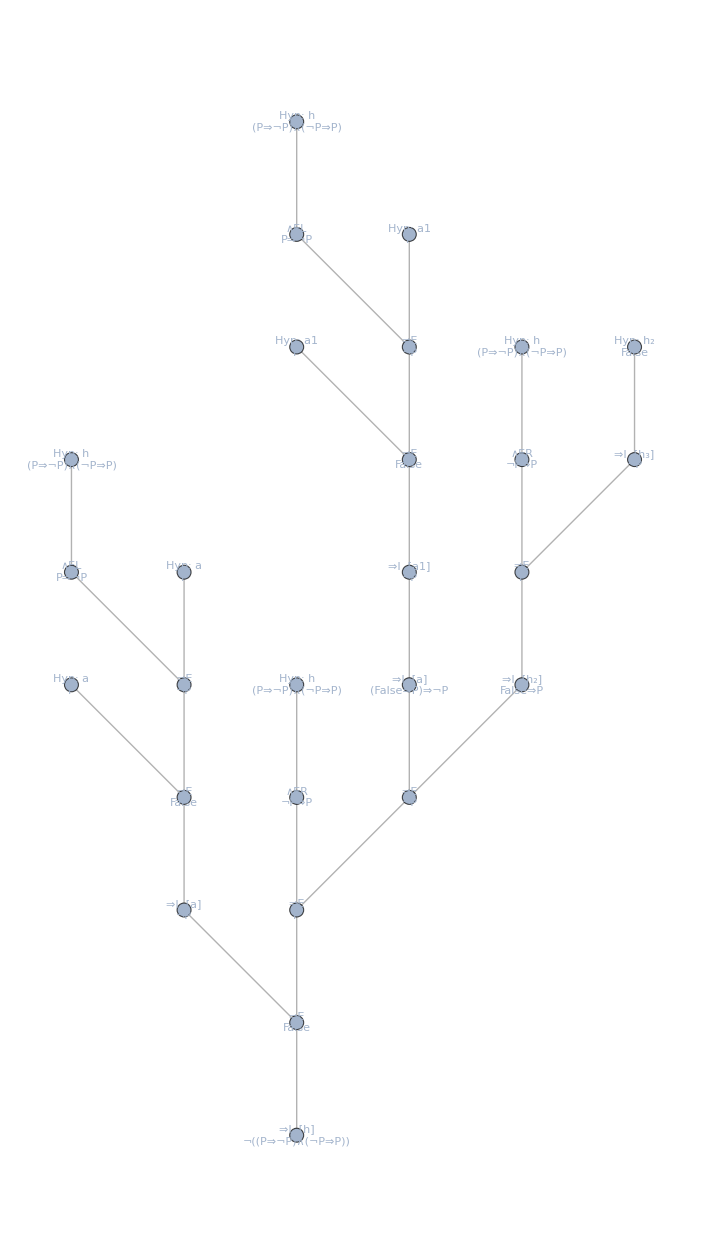

```mathematica
DiagramOfFormula[ForAll[{P},Not[And[Implies[P,Not[P]],Implies[Not[P],P]]]],{P}]
```

```mathematica
<<"CICTranslate.m"
```

```mathematica
RunLeanTactic[LambdaFunction[Alpha,LambdaFunction[Typed[x,Alpha],x]],"elaborate",True]//ToExpression // CICTranslate
```

LambdaFunction[Typed[Alpha,StarType],LambdaFunction[Typed[x,Alpha],x]]

```mathematica
RunLeanTactic[LambdaFunction[Alpha,LambdaFunction[Typed[x,Alpha],x]],"type_check",True]//ToExpression // CICTranslate
```

PiType[Typed[Alpha,StarType],PiType[Typed[x,Alpha],Alpha]]

```mathematica
RunLeanTactic[ForAllTyped[{s,t,u},set[nat],SetUnion[s,SetUnion[t,u]]==SetUnion[SetUnion[u,s],t]],"normalize_set_lemmas"]
```

set.union_comm : ∀ {α : Type ?} (a b : set α), a ∪ b = b ∪ a
set.union_assoc : ∀ {α : Type ?} (a b c : set α), a ∪ b ∪ c = a ∪ (b ∪ c)

```mathematica
RunLeanTactic[ForAllTyped[{x,y},real,Implies[x<y,Exists[{z},And[x<z, z<y]]]],"find_relevant_facts","imports"]
```

Syntax::sntx: Invalid syntax in or before "/home/rlewis/Dropbox/lean/mm_lean/temp.lean:1:0: error: invalid import: data.seq.computation" (line 2 of "/tmp/m000008280471").
                                            ^

ennreal.densely_ordered._match_1 : ∀ (r : ℝ),
  0 ≤ r →
  ∀ (p : ℝ),
    0 ≤ p →
    (∃ (a : ℝ), r < a ∧ a < p) → (∃ (a : ennreal), a < ennreal.of_real p ∧ ennreal.of_real r < a)
ennreal.densely_ordered.equations._eqn_1 : ennreal.densely_ordered = _
measure_theory.outer_measure.of_function._match_2 : ∀ {α : Type ?} (m : set α → ennreal) (s : ℕ → set α) (ε : ℝ),
  ε > 0 →
  (∃ (f : Π (x : ℕ), (λ (i : ℕ), ℕ → set α) x),
     ∀ (x : ℕ),
       (λ (i : ℕ) (f : ℕ → set α),
          s i ⊆ ∪ (i : ℕ), f i ∧
            (∑ (i : ℕ), m (f i)) <
              (λ (s : set α), ⨅ {f : ℕ → set α} (h : s ⊆ ∪ (i : ℕ), f i), ∑ (i : ℕ), m (f i)) (s i) +
                ennreal.of_real ((λ (i : ℕ), ε / 2 * 2⁻.b9 ^ i) i))
         x
         (f x)) →
  (λ (s : set α), ⨅ {f : ℕ → set α} (h : s ⊆ ∪ (i : ℕ), f i), ∑ (i : ℕ), m (f i))
      (∪ (i : ℕ), s i) ≤
    (∑ (i : ℕ),
         (λ (s : set α), ⨅ {f : ℕ → set α} (h : s ⊆ ∪ (i : ℕ), f i), ∑ (i : ℕ), m (f i)) (s i)) +
      ennreal.of_real ε
ennreal.densely_ordered._match_1.equations._eqn_1 : ∀ (r : ℝ) (hr : 0 ≤ r) (p : ℝ) (hp : 0 ≤ p) (q : ℝ) (h₁ : r < q) (h₂ : q < p), _ = _
exists_lt_of_rat_of_rat_gt : ∀ {r p : ℝ}, r < p → (∃ (q : ℚ), r < of_rat q ∧ of_rat q < p)
real.metric_space._match_1 : ∀ (ε : ℝ),
  (∃ (q : ℚ), 0 < q ∧ of_rat q < ε) →
  (∃ (e : ℚ) (H : e > 0),
     ∀ (r₁ r₂ : ℝ),
       abs (r₁ - r₂) < of_rat e → (r₁, r₂) ∈ {p : ℝ × ℝ | abs (p.fst - p.snd) < ε})
real.metric_space._match_1.equations._eqn_1 : ∀ (ε : ℝ) (q : ℚ) (hq₁ : 0 < q) (hq₂ : of_rat q < ε), _ = _
ennreal.topological_add_monoid.equations._eqn_1 : ennreal.topological_add_monoid = _
ennreal.lt_iff_exists_of_real : ∀ {a b : ennreal}, a < b ↔ ∃ (p : ℝ), 0 ≤ p ∧ a = ennreal.of_real p ∧ ennreal.of_real p < b
exists_pos_of_rat : ∀ {r : ℝ}, 0 < r → (∃ (q : ℚ), 0 < q ∧ of_rat q < r)